```mathematica
ExportDataSetToCSV[filename_,data_]:=Module[{result ,rowname,colname,mat},
rowname =Keys[data]//Normal;
colname =  Keys[data[[1]]]//Normal;
PrependTo[rowname,"FIPS"];

mat= data//Values//Normal//Values; (* extract the values and return a matrix *)
PrependTo[mat,colname];
result= Join[List /@ rowname,mat,2];

Export[filename,result];
];
```

```mathematica
l1 = SwatchLegend[{Black,Gray,Orange},Style[#, 12,FontFamily->"Helvetica"]& /@{"Irrigated","Non-irrigated","All practices"}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/legend1.jpg",l1, ImageResolution->600]
```

/Users/gola/Box Sync/projects/ACES_ag_trends/figs/legend1.jpg

```mathematica
fr = Frame->{{True,False},{True,False}};
```

```mathematica
NAME = {"corn_irr","corn_non","corn_unc","soy_irr","soy_non","soy_unc","wheat_irr","wheat_non","wheat_unc"};
CROP = {"corn","soy","wheat"}; CAT = {"_irr","_non","_unc"};
```

## Data compile: unc = All practices from the manuscript

### Crop

```mathematica
CROP = {"corn","soy","wheat"};
```

```mathematica
cy1 = Import["/your_directory/raw/raw_corn_yield_1970.csv"];
cy2 = Import["/your_directory/raw/raw_corn_yield_1985.csv"][[2;;]];
cy3 = Import["/your_directory/raw/raw_corn_yield_2000.csv"][[2;;]];

CY = Join[cy1,cy2,cy3];
sy1 = Import["/your_directory/raw/raw_soy_yield_1970.csv"];
sy2 = Import["/your_directory/raw/raw_soy_yield_1993.csv"][[2;;]];

SY = Join[sy1,sy2];

wy1 = Import["/your_directory/raw/raw_wheat_yield_1970.csv"];
wy2 = Import["/your_directory/raw/raw_wheat_yield_1980.csv"][[2;;]];
wy3 = Import["/your_directory/raw/raw_wheat_yield_1990.csv"][[2;;]];
wy4 = Import["/your_directory/raw/raw_wheat_yield_2000.csv"][[2;;]];
wy5 = Import["/your_directory/raw/raw_wheat_yield_2010.csv"][[2;;]];

WY = Join[wy1,wy2,wy3,wy4,wy5];

ALLDAT = AssociationThread[CROP,{CY,SY,WY}];
```

```mathematica
(* Loop through all crops *)
Do[
DAT = ALLDAT[crop];

sDAT = DAT[[2;;,{17, 2,7,11, -2}]]; (* on select the needed info, irrigation type, year, ANSI for state and county, value *)
sDAT[[All,3]] = sDAT[[All,3]]*1000 + sDAT[[All,4]]; (* creates the FIPS *)
sDAT= Drop[sDAT,0,{4}]; (* drop the column for the ANSI county *)
sDAT = Select[sDAT,NumericQ[#[[3]]]== True &]; (* remove other counties that has non-numeric FIPS, due to missing count ANSI *)
sDAT[[All,-1]] *= If[crop =="corn",62.77, 67.25]; (* convert from bu/ac to kg/ha, Chris gave those values *)
gDAT = GroupBy[sDAT,First]; (* group with respect to the irrigation category *)

KYS = Keys[gDAT]; 

(* Loop through all irrigation category *)
Do[
sub = gDAT[kys];
LL = Length@sub;
FIPS = ToString /@ Sort@Union[sub[[All,3]]]; (*Extract all unique FIPS *)
base = Table[FIPS[[i]]-> AssociationThread[ToString /@Range[1970,2017],ConstantArray["NA",48]],{i,Length@FIPS}]//Association; (* construct a sparse array with 2 keys: FIPS and YEAR *)

(* loop through all rows in the matrix *)
Do[
vect = sub[[l]];
kF = ToString@vect[[3]]; (* get FIPS *)
kY = ToString@vect[[2]]; (* get year *)
value = vect[[-1]]/.{0. -> "NA"}; (* get yield and replace  0 by "NA" *)
base[kF,kY]=value; (* assign to the sparse array*)
,{l,LL}];

(* Export the compiled data *)
Which[
StringContainsQ[kys,", IRRIGATED"] == True,Export["/your_directory/raw/"<>crop<>"_irr.m",base],
StringContainsQ[kys,", NON-IRRIGATED"] == True, Export["/your_directory/raw/"<>crop<>"_non.m",base],
StringContainsQ[kys,", NON-IRRIGATED" | ", IRRIGATED"] == False  , Export["/your_directory/raw/"<>crop<>"_unc.m",base]
];
,{kys,KYS}];
,{crop,CROP}];
```

### Area planted

```mathematica
cp1 = Import["/your_directory/raw/raw_corn_planted_1970.csv"];
cp2 = Import["/your_directory/raw/raw_corn_planted_1985.csv"][[2;;]];
cp3 = Import["/your_directory/raw/raw_corn_planted_2000.csv"][[2;;]];

CP = Join[cp1,cp2,cp3];

sp1 = Import["/your_directory/raw/raw_soy_planted_1970.csv"];
sp2 = Import["/your_directory/raw/raw_soy_planted_1993.csv"][[2;;]];

SP = Join[sp1,sp2];

wp1 = Import["/your_directory/raw/raw_wheat_planted_1970.csv"];
wp2 = Import["/your_directory/raw/raw_wheat_planted_1975.csv"][[2;;]];
wp3 = Import["/your_directory/raw/raw_wheat_planted_1985.csv"][[2;;]];
wp4 = Import["/your_directory/raw/raw_wheat_planted_1996.csv"][[2;;]];

WP = Join[wp1,wp2,wp3,wp4];

ALLDAT = AssociationThread[CROP,{CP,SP,WP}];
```

```mathematica
(* Loop through all crops *)
Do[
DAT = ALLDAT[crop];

sDAT = DAT[[2;;,{17, 2,7,11, -2}]]; (* on select the needed info, irrigation type, year, ANSI for state and county, value *)
sDAT[[All,3]] = sDAT[[All,3]]*1000 + sDAT[[All,4]]; (* creates the FIPS *)
sDAT= Drop[sDAT,0,{4}]; (* drop the column for the ANSI county *)
sDAT = Select[sDAT,NumericQ[#[[3]]]== True &]; (* remove other counties that has non-numeric FIPS, due to missing count ANSI *)
gDAT = GroupBy[sDAT,First]; (* group with respect to the irrigation category *)

KYS = Keys[gDAT]; 

(* Loop through all irrigation category *)
Do[
sub = gDAT[kys];
LL = Length@sub;
FIPS = ToString /@ Sort@Union[sub[[All,3]]]; (*Extract all unique FIPS *)
base = Table[FIPS[[i]]-> AssociationThread[ToString /@Range[1970,2017],ConstantArray["NA",48]],{i,Length@FIPS}]//Association; (* construct a sparse array with 2 keys: FIPS and YEAR *)

(* loop through all rows in the matrix *)
Do[
vect = sub[[l]];
kF = ToString@vect[[3]]; (* get FIPS *)
kY = ToString@vect[[2]]; (* get year *)
value = vect[[-1]]; (* get yield *)
base[kF,kY]=value; (* assign to the sparse array*)
,{l,LL}];

(* Export the compiled data *)
Which[
StringContainsQ[kys,", IRRIGATED"] == True, Export["/your_directory/raw/"<>crop<>"_planted_irr.m",base],
StringContainsQ[kys,", NON-IRRIGATED"] == True, Export["/your_directory/raw/"<>crop<>"_planted_non.m",base],
StringContainsQ[kys,", NON-IRRIGATED" | ", IRRIGATED"] == False  , Export["/your_directory/raw/"<>crop<>"_planted_unc.m",base]
];
,{kys,KYS}];
,{crop,CROP}];
```

### Area harvested (not run)

```mathematica
ch1 = Import["/your_directory/raw/raw_corn_harvested_1970.csv"];
ch2 = Import["/your_directory/raw/raw_corn_harvested_1985.csv"][[2;;]];
ch3 = Import["/your_directory/raw/raw_corn_harvested_2000.csv"][[2;;]];

CH = Join[ch1,ch2,ch3];

sh1 = Import["/your_directory/raw/raw_soy_harvested_1970.csv"];
sh2 = Import["/your_directory/raw/raw_soy_harvested_1980.csv"][[2;;]];
sh3 = Import["/your_directory/raw/raw_soy_harvested_1995.csv"][[2;;]];

SH = Join[sh1,sh2,sh3];

wh1 = Import["/your_directory/raw/raw_wheat_harvested_1970.csv"];
wh2 = Import["/your_directory/raw/raw_wheat_harvested_1980.csv"][[2;;]];
wh3 = Import["/your_directory/raw/raw_wheat_harvested_1986.csv"][[2;;]];
wh4 = Import["/your_directory/raw/raw_wheat_harvested_2000.csv"][[2;;]];

WH = Join[wh1,wh2,wh3,wh4];

ALLDAT = AssociationThread[CROP,{CH,SH,WH}];
```

```mathematica
(* Loop through all crops *)
Do[
DAT = ALLDAT[crop];

sDAT = DAT[[2;;,{17, 2,7,11, -2}]]; (* on select the needed info, irrigation type, year, ANSI for state and county, value *)
sDAT[[All,3]] = sDAT[[All,3]]*1000 + sDAT[[All,4]]; (* creates the FIPS *)
sDAT= Drop[sDAT,0,{4}]; (* drop the column for the ANSI county *)
sDAT = Select[sDAT,NumericQ[#[[3]]]== True &]; (* remove other counties that has non-numeric FIPS, due to missing count ANSI *)
gDAT = GroupBy[sDAT,First]; (* group with respect to the irrigation category *)

KYS = Keys[gDAT]; 

(* Loop through all irrigation category *)
Do[
sub = gDAT[kys];
LL = Length@sub;
FIPS = ToString /@ Sort@Union[sub[[All,3]]]; (*Extract all unique FIPS *)
base = Table[FIPS[[i]]-> AssociationThread[ToString /@Range[1970,2017],ConstantArray["NA",48]],{i,Length@FIPS}]//Association; (* construct a sparse array with 2 keys: FIPS and YEAR *)

(* loop through all rows in the matrix *)
Do[
vect = sub[[l]];
kF = ToString@vect[[3]]; (* get FIPS *)
kY = ToString@vect[[2]]; (* get year *)
value = vect[[-1]]; (* get yield *)
base[kF,kY]=value; (* assign to the sparse array*)
,{l,LL}];

(* Export the compiled data *)
Which[
StringContainsQ[kys,", IRRIGATED"] == True, Export["/your_directory/raw/"<>crop<>"_harvested_irr.m",base],
StringContainsQ[kys,", NON-IRRIGATED"] == True, Export["/your_directory/raw/"<>crop<>"_harvested_non.m",base],
StringContainsQ[kys,", NON-IRRIGATED" | ", IRRIGATED"] == False  , Export["/your_directory/raw/"<>crop<>"_harvested_unc.m",base]
];
,{kys,KYS}];
,{crop,CROP}];
```

## Data clean and export

```mathematica
(* return true if the vector satisfies the criteria *)
AcceptData[vect_, plant_]:=Module[{result,kp,cvect,yr, len,maxgap,lastyr},
kp = Select[plant,( # < 1000. || # == "NA") &]//Keys; (* years with planted area less than 1000 ac or NA  *)
kp  = Partition[ToString /@kp,1];

cvect = Select[vect,# ≠ "NA"&]; (* remove NA  *)
cvect = Delete[cvect,kp]; (* remove year when planted area is less than 1000 ac or NA *)

yr = cvect //Keys//ToExpression; (* years with sufficient yield  *)

len = cvect//Length; (* total number of points *)
maxgap = yr//Differences//Max; (* maximum missing points between successive year *)
lastyr = yr//Max; (* last data *)

result = If[ len ≥ 15 && lastyr ≥ 2000 &&  maxgap <10,True,False];

result];
```

```mathematica
ALLMEAN = {}; 
Do[
yield =  Import["/your_directory/raw/"<>crop<>cat<>".m"];
plant=  Import["/your_directory/raw/"<>crop<>"_planted"<>cat<>".m"];
KEYS = yield//Keys;
CLEAN = {};
Do[
vect1 = yield[k] ;
vect2 = plant[k]; 
If[MissingQ[vect2]==True, Continue[]];

accept = AcceptData[vect1,vect2];
If[accept ==False,Continue[]];

(* clean the vector for export *)
kp = Select[vect2, (# == "NA" ||# < 1000.)&]//Keys;
Do[ vect1[i] = "NA",{i,kp}]; (* remove points when area planted is not reported or less than 1000 ac *)
 cleany = k-> vect1 ;
AppendTo[CLEAN,cleany];
,{k,KEYS}];
CLEAN = CLEAN//Association//Dataset;
(* export as mathematica file*)
Export["/your_directory/clean/clean_"<>crop<>cat<>".m",CLEAN];
(* export to use for other program (R) *)
outname = "/your_directory/clean/clean_"<>crop<>cat<>".csv";
ExportDataSetToCSV[outname,CLEAN];

(* compute the mean per year
- The first () select numeric values in CLEAN (by column) and compute the mean
- The second () loop through all columns *)
mean = (Mean[ Cases[#, _?NumericQ] &//CLEAN[All,#]]) &/@ (ToString /@ Range[1970,2017]);
mean = mean  /. Mean[{}]-> "NA" //Flatten;
AppendTo[ALLMEAN,{crop<>cat,mean}//Flatten];

,{crop,CROP},{cat, CAT}];
```

```mathematica
Export["/your_directory/clean/all_mean.csv",ALLMEAN]
```

```mathematica
"/Users/gola/Box Sync/projects/ACES_ag_trends/data/clean/all_mean.csv"
```

## Summary data

```mathematica
allFIPS = Table[Import["/your_directory/clean/clean_"<>crop<>cat<>".m"]//Keys//Normal,{crop,CROP},{cat,CAT}]//Flatten;
```

```mathematica
allFIPS//Union//Length
```

2290

```mathematica
IntegerPart[Union[ToExpression@allFIPS]/1000.]//Union//Length
```

42

```mathematica
dat = Import["/your_directory/clean/clean_corn_unc_fit_coeff.csv"][[2;;-2,{2,3,4,5}]];
```

```mathematica
tal = Tally[dat[[All,1]]]
```

{{1,381},{0,1531}}

```mathematica
tal[[2,2]]/Total[tal[[All,2]]]//N
```

0.800732

```mathematica
nc1 = Select[dat,#[[2]]<0 &]//Length
```

19

```mathematica
pc2 = Select[dat,#[[4]]>0 &]//Length
```

264

```mathematica
nc2 = Select[dat,#[[4]]<0 &]//Length
```

117

```mathematica
dat = Import["/your_directory/clean/clean_soy_unc_fit_coeff.csv"][[2;;-2,{2,3,4,5}]];
```

```mathematica
tal = Tally[dat[[All,1]]]
```

{{1,362},{0,1185}}

```mathematica
tal[[2,2]]/Total[tal[[All,2]]]//N
```

0.765999

```mathematica
nc1 = Select[dat,#[[2]]<0 &]//Length
```

19

```mathematica
pc2 = Select[dat,#[[4]]>0 &]//Length
```

317

```mathematica
nc2 = Select[dat,#[[4]]<0 &]//Length
```

45

```mathematica
dat = Import["/your_directory/clean/clean_wheat_unc_fit_coeff.csv"][[2;;-2,{2,3,4,5}]];
```

```mathematica
tal = Tally[dat[[All,1]]]
```

{{0,1357},{1,348}}

```mathematica
tal[[1,2]]/Total[tal[[All,2]]]//N
```

0.795894

```mathematica
nullc1 = Select[dat,-20 ≤ #[[2]]≤ 20 &]//Length
```

426

```mathematica
nc1 = Select[dat,#[[2]]<0 &]//Length
```

39

```mathematica
pc2 = Select[dat,#[[4]]>0 &]//Length
```

192

```mathematica
nc2 = Select[dat,#[[4]]<0 &]//Length
```

156

## Figure 1 (first column) national trend

```mathematica
PARAM = Import["/your_directory/clean/fit_mean.csv"];
ALLMEAN =Import["/your_directory/clean/all_mean.csv"];
```

```mathematica
FIT[x_, param_]:= param[[1]] + param[[2]] x + param[[3]] x^2;
```

```mathematica
NAME
```

{corn_irr,corn_non,corn_unc,soy_irr,soy_non,soy_unc,wheat_irr,wheat_non,wheat_unc}

```mathematica
PS = ConstantArray[ {Black,Gray,Orange},3]//Flatten;
clbx = Range[1,48,10];
clby =Style[#, White]&  /@ToString /@ Range[1970,2017,10];
tx ={clbx,clby}//Transpose;
pr = PlotRange-> {All,{0,All}};
ip = ImagePadding->{{20,5},{5,0}};
```

```mathematica
F1  =Table[
Show[ListPlot[ALLMEAN[[i]]/1000,PlotStyle->PS[[i]],pr,Axes->False],Plot[FIT [x, Evaluate[PARAM[[ i+1,2;;]]/1000]],{x,0,48} ,PlotStyle->PS[[i]]],Frame->True,FrameTicks->{{Automatic,None}, {tx,False}},PlotRangePadding->Scaled[.05],ImageSize-> 2.5 72,ip],{i,9}];
```

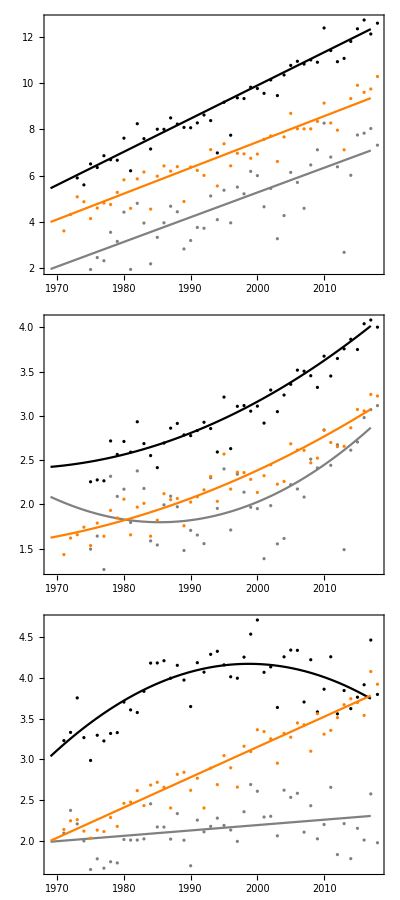

```mathematica
F1C1 = Grid[Transpose@{{Show[F1[[1;;3]],PlotRange->All],Show[F1[[4;;6]],PlotRange->All],Show[F1[[7;;9]],PlotRange->All]}},Spacings->{0,1}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1c1.pdf",F1C1]
```

/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1c1.pdf

## Figure 1 (second column) variability

```mathematica
On[Assert];
```

```mathematica
(* Compute the standard deviation of the residuals per decade, part: partitions the data *)
DevianceDecadeSD[vect_,part_]:=Module[{result = {},i0,i1,v,sv,sd},
Do[
i0 = i[[1]];
i1 = i[[2]];
v = vect[[i0;;i1]];
sv =Cases[v,_?NumericQ]; (* drops missing data, residual  = NA *)
sd = If[Length@sv < 2, "NA",StandardDeviation@sv]; (* compute the standard deviation *)
AppendTo[result,sd];
,{i,part}];
result]
```

### Standard deviation decade % residuals

```mathematica
(* compute the deviance per decade *)
PART2 = {{1,10},{11,20},{21,29},{30,39},{40,48}};
colname = {"FIPS","70-79","80-89","90-99","00-09","10-17"};
Do[
sig = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{1,2}]];

lin = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_res_lin_s.csv"][[All,2;;]];
quad= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_res_quad_s.csv"][[All,2;;]];

LL = Length@sig;
VECT = ConstantArray[{},LL];
Do[
fips = sig[[l,1]];
s = sig[[l,2]];
vect = If[s ==0, lin[[l]],quad[[l]] ];
res = DevianceDecadeSD[vect,PART2];
PrependTo[res,fips];
VECT[[l]] =res;
,{l,LL}];
PrependTo[VECT,colname];
Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_sd_decade_s.csv",VECT];
,{i,9}];
```

```mathematica
HH  = {};
Do[
hh = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_sd_decade_s.csv"][[2;;,2;;]];
thh = Transpose[hh];
AppendTo[HH,thh];
,{i,9}];
VV = HH;
```

```mathematica
VV//Length
```

9

```mathematica
NAME
```

{corn_irr,corn_non,corn_unc,soy_irr,soy_non,soy_unc,wheat_irr,wheat_non,wheat_unc}

```mathematica
(*Change relative to 1970-79*)
MVV= {};
Do[
mvv = {};
Do[
vv = DeleteCases[VV[[i,j]], "NA"];
tm = Median[vv];
If[j==1, 
mv0 = tm,
AppendTo[mvv,Round[100 (tm - mv0)/mv0]]
];
,{j,5}];
AppendTo[MVV,mvv];
,{i,9}]
```

```mathematica
MVV
```

{{29,47,-11,-18},{22,-13,-1,14},{21,-2,-11,-9},{-2,12,-22,-40},{-7,5,6,-2},{14,1,15,-14},{14,9,26,15},{21,6,19,18},{13,13,5,-7}}

```mathematica
(*Change relative to the preceding decade*)
MVV= {};
Do[
mvv = {};
Do[
vv = DeleteCases[VV[[i,j]], "NA"];
tm = Median[vv];
If[j==1, 
mv0 = tm,
AppendTo[mvv,Round[100 (tm - mv0)/mv0]];
mv0 = tm;
];
,{j,5}];
AppendTo[MVV,mvv];
,{i,9}]
```

```mathematica
MVV
```

{{29,14,-39,-8},{22,-29,15,15},{21,-19,-8,2},{-2,15,-30,-23},{-7,13,1,-8},{14,-11,13,-25},{14,-5,15,-8},{21,-13,12,-1},{13,1,-8,-11}}

```mathematica
cs = ChartStyle->{Black,Gray,Orange};
(*cs1= ChartStyle->Orange;
cs2= ChartStyle->Black;
cs3= ChartStyle->Gray;*)
pr2 = PlotRange->{All,{0,100}};
```

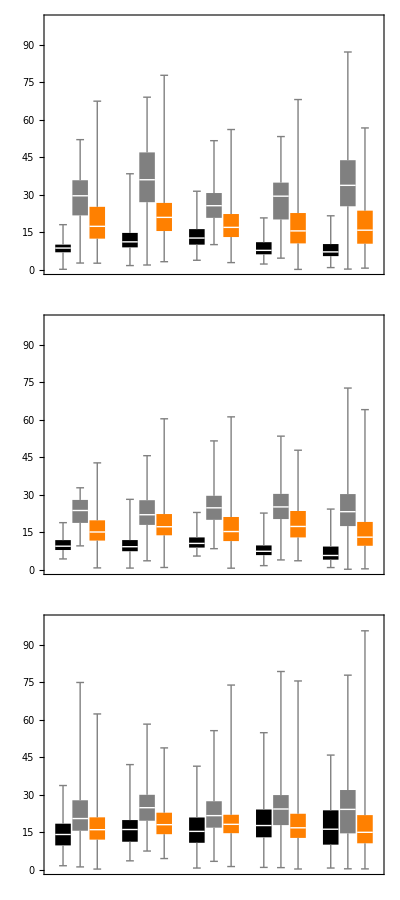

```mathematica
F1C2 =Grid[{{BoxWhiskerChart[VV[[{1,2,3}]]//Transpose,BarSpacing->{0.1,1},cs,pr2],BoxWhiskerChart[VV[[{4,5,6}]]//Transpose,BarSpacing->{0.1,1},cs,pr2],BoxWhiskerChart[VV[[{7,8,9}]]//Transpose,BarSpacing->{0.1,1},cs,pr2]}}//Transpose,Spacings->{0,1.25}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1c2.pdf",F1C2]
```

/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1c2.pdf

### Standard deviation decade absolute residuals

```mathematica
(* compute the deviance per decade *)
PART2 = {{1,10},{11,20},{21,29},{30,39},{40,48}};
colname = {"FIPS","70-79","80-89","90-99","00-09","10-17"};
Do[
sig = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{1,2}]];

lin = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_res_lin.csv"][[All,2;;]];
quad= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_res_quad.csv"][[All,2;;]];

LL = Length@sig;
VECT = ConstantArray[{},LL];
Do[
fips = sig[[l,1]];
s = sig[[l,2]];
vect = If[s ==0, lin[[l]],quad[[l]] ];
res = DevianceDecadeSD[vect,PART2];
PrependTo[res,fips];
VECT[[l]] =res;
,{l,LL}];
PrependTo[VECT,colname];
Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_sd_decade.csv",VECT];
,{i,9}];
```

```mathematica
HH  = {};
Do[
hh = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_sd_decade.csv"][[2;;,2;;]]/1000;
thh = Transpose[hh];
AppendTo[HH,thh];
,{i,9}]
```

```mathematica
cs = ChartStyle->{Orange, Black,Gray};
cs1= ChartStyle->Orange;
cs2= ChartStyle->Black;
cs3= ChartStyle->Gray;
pr ={ PlotRange->{All,{0,4.200}}, PlotRange->{All,{0,1.600}}, PlotRange->{All,{0,2.500}}};
```

```mathematica
ip = ImagePadding->{{20,5},{5,0}};
```

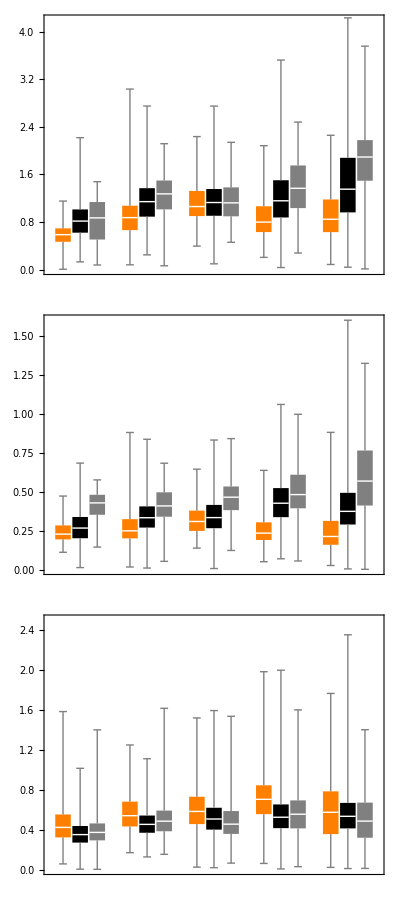

```mathematica
FIGREL =Grid[{{BoxWhiskerChart[HH[[{1,3,2}]]//Transpose,BarSpacing->{0.1,1},cs,pr[[1]],ip],BoxWhiskerChart[HH[[{4,6,5}]]//Transpose,BarSpacing->{0.1,1},cs,pr[[2]],ip],BoxWhiskerChart[HH[[{7,9,8}]]//Transpose,BarSpacing->{0.1,1},cs,pr[[3]],ip]}}//Transpose,Spacings->{0,1.25}]
```

### Recycle if a need for standard error

```mathematica
ME =SE =  {};
Do[
hh = Import["~/Desktop/clean_"<>NAME[[i]]<>"_sd_decade.csv"][[2;;,2;;]];
thh = Transpose[hh];
vv = Cases[#, _?NumericQ] &/@thh;
me =Mean /@ vv;
se = (StandardDeviation /@ vv)  / (Sqrt[Length /@ vv]);

AppendTo[ME,me];
AppendTo[SE,se];
,{i,9}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

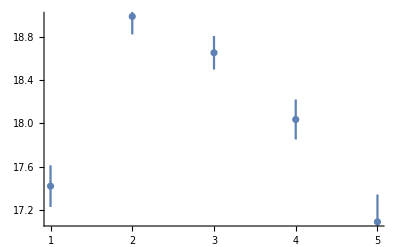

```mathematica
i = 9;
gg = Partition[Riffle[ME[[i]], SE[[i]]] ,2];
ErrorListPlot[gg,PlotRange->All]
```

### Recycle for plot without fences

```mathematica
HH  = {};
Do[
hh = Import["/your_directory/clean_"<>NAME[[i]]<>"_dev_decade_mean.csv"][[2;;,2;;]];
thh = Transpose[hh];
AppendTo[HH,thh];
,{i,9}]
```

```mathematica
hh  =hh//Transpose;
```

```mathematica
cs = ChartStyle->{Orange, Black,Gray};
cs1= ChartStyle->Orange;
cs2= ChartStyle->Black;
cs3= ChartStyle->Gray;
```

```mathematica
Grid[
{
{BoxWhiskerChart[HH[[{1,3,2}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs,PlotRange-> {All,{0.02,0.33}},BarSpacing->{0.1,1}],
BoxWhiskerChart[HH[[{4,6,5}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs,PlotRange->  {All,{0.02,0.33}},BarSpacing->{0.1,1}],
BoxWhiskerChart[HH[[{7,9,8}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs,PlotRange->  {All,{0.02,0.33}},BarSpacing->{0.1,1}]},
{BoxWhiskerChart[HH[[{1,4,7}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs1,PlotRange-> {All,{0.02,0.33}},BarSpacing->{0.1,1}],
BoxWhiskerChart[HH[[{3,6,9}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs2,PlotRange->  {All,{0.02,0.33}},BarSpacing->{0.1,1}],
BoxWhiskerChart[HH[[{2,5,8}]]//Transpose, {{"Fences",0,None},{"Whiskers",Opacity[0]}},cs3,PlotRange->  {All,{0.02,0.33}},BarSpacing->{0.1,1}]}
}];
```

## Figure 1 (third column) yield gap

```mathematica
PART =1+ {{1,10},{11,20},{21,29},{30,38},{39,48}}; (* the +1 is to shift by one element as the first element is FIPS *)
```

```mathematica
(* return the yeild gap per time period defined by part 
- dat  is a vector, first element is FIPS, the remaining 48 elements are yield 
- part partitions the vector, part should be actual index (not year) 
- the output is the a vector, the first element is FIPS and the remaining elements are yield gap within a time period *)
YieldGap[dat_,part_]:=Module[{result = {dat[[1]]},temp,sub,i0,i1},
Do[
i0 = i[[1]];
i1 = i[[2]];
sub =  DeleteCases[dat[[i0;;i1]],"NA"];
temp = If[Length@sub>1,
 Mean@sub - Max@sub,
 "NA"
];
AppendTo[result,temp];
,{i,part}];
result];

CreateExtreme[v1_,v2_]:=Module[{result,v3,max,min},
v3 = v1 -v2;
max = Max[Cases[v3,_?NumericQ]]; 
min = Min[Cases[v3,_?NumericQ]]; 
result  =If[Abs[max]> Abs[min],-max, -min ];
result];
```

```mathematica
(* Calculating maximum yield per decade*)
MAX = {};
PT = {{1,10},{11,20},{21,29},{30,38},{39,48}};
Do[
d1= Import["/your_directory/clean/clean_"<>NAME[[i]]<>".csv"][[2;;,2;;]];
d2= Import["/your_directory/clean/clean_"<>NAME[[i+1]]<>".csv"][[2;;,2;;]];
d3 = Import["/your_directory/clean/clean_"<>NAME[[i+2]]<>".csv"][[2;;,2;;]];

M = {};
Do[
pt = PT[[j,1]];;PT[[j,2]];
q1 =DeleteCases[Flatten [{d1[[All,pt]],d2[[All,pt]],d3[[All,pt]]}],"NA"];
Q1 = Quantile[q1, 0.9999];
AppendTo[M,Q1];
,{j,5}];
AppendTo[MAX,M];
,{i,{1,4,7}}];
```

```mathematica
MAX
```

{{8599.49,10608.1,11775.7,12823.9,13897.3},{2891.75,3234.73,3698.75,4035.,4539.38},{5649.,6772.08,7424.4,7901.88,7868.25}}

```mathematica
MAX
```

{{10175.,12924.3,13872.2,14468.5,16031.5},{3026.25,3564.25,4102.25,4505.75,4983.22},{7061.25,7821.18,8715.6,9213.25,9468.8}}

```mathematica
(* this one is for  exporting data to make it symmetric and adding a column of yield gap between the first and last decade*)
FIG= {};
colname = {"FIPS","1970-79","1980-89","1990-98","1999-07","2008-17","ygap_diff"};
Do[
data = Import["/your_directory/clean/clean_"<>NAME[[i]]<>".csv"][[2;;]];

LL = Length@data;
DATA = ConstantArray["NA",{LL,6}];
Do[
dt  = data[[l, 2;;]];
DATA[[l,1]]= data[[l,1]]; (* add FIPS code *)
Do[
pt = PT[[j,1]];;PT[[j,2]];
decdat = DeleteCases[dt[[pt]],"NA"];(* all raw data during the decade *)
If[Length@decdat ==0,
Continue[],
row  = Ceiling[i/3];
yieldgap = Mean[decdat]  - MAX[[row, j]];
DATA[[l,j+1]] = yieldgap/1000; (* convert to Mg *)
];
,{j,5}];
,{l, LL}];

v1 = DATA[[All,2]];
v2 = DATA[[All,-1]];

 MAXDIFF = CreateExtreme[v1,v2];

diffcol = (Replace[v1  -v2,Except[_?NumericQ]->"NA",{1}]) /. 0 -> "NA";

DATA = MapThread[Append,{DATA,diffcol}];

MAXYG = Min@Min[DeleteCases[DATA[[All,{2,-2}]],"NA",2]];
PrependTo[DATA,colname];
AppendTo[DATA,{2185, MAXYG,MAXYG,MAXYG,MAXYG,MAXYG,MAXDIFF }];

Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap_995.csv",DATA];
,{i,9}];
```

```mathematica
YG = Grid[Partition[FIG,3]];
```

```mathematica
HH  = {};
Do[
hh = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap.csv"][[2;;-2,2;;-2]];
thh = Transpose[hh];
AppendTo[HH,thh];
,{i,9}]
```

```mathematica
NAME
```

{corn_irr,corn_non,corn_unc,soy_irr,soy_non,soy_unc,wheat_irr,wheat_non,wheat_unc}

```mathematica
(*Change relative to the 1970-79*)
MYG= {};
Do[
myg = {};
Do[
yg = DeleteCases[HH[[i,j]], "NA"];
tm = Median[yg];
If[j==1, 
yg0 = tm,
AppendTo[myg,Round[100 (tm - yg0)/yg0]];
];
,{j,5}];
AppendTo[MYG,myg];
,{i,9}]
```

```mathematica
MYG
```

{{48,49,20,30},{23,18,25,22},{39,41,34,38},{66,110,113,126},{46,80,132,92},{33,47,67,69},{8,26,36,41},{9,24,31,35},{9,22,23,20}}

```mathematica
(*Change relative to the preceding decade*)
MYG= {};
Do[
myg = {};
Do[
yg = DeleteCases[HH[[i,j]], "NA"];
tm = Median[yg];
If[j==1, 
yg0 = tm,
AppendTo[myg,Round[100 (tm - yg0)/yg0]];
yg0 = tm;
];
,{j,5}];
AppendTo[MYG,myg];
,{i,9}]
```

```mathematica
MYG
```

{{48,1,-20,9},{23,-4,6,-2},{39,1,-5,3},{66,27,1,6},{46,23,29,-17},{33,11,14,1},{8,17,8,4},{9,13,5,3},{9,13,0,-2}}

```mathematica
test = Import["/your_directory/gz_2010_us_050_00_20m_county/clean_corn_non_ygap.csv"][[2;;,2;;-2]];
```

```mathematica
Max[test]
```

Max[-62.77,NA]

```mathematica
Min[test]
```

Min[-4029.83,NA]

```mathematica
cs = ChartStyle->{ Black,Gray,Orange};
(*cs1= ChartStyle->Orange;
cs2= ChartStyle->Black;
cs3= ChartStyle->Gray;*)
pr3 ={ PlotRange->{All,Automatic}, PlotRange->{All,Automatic}, PlotRange->{All,Automatic}};
```

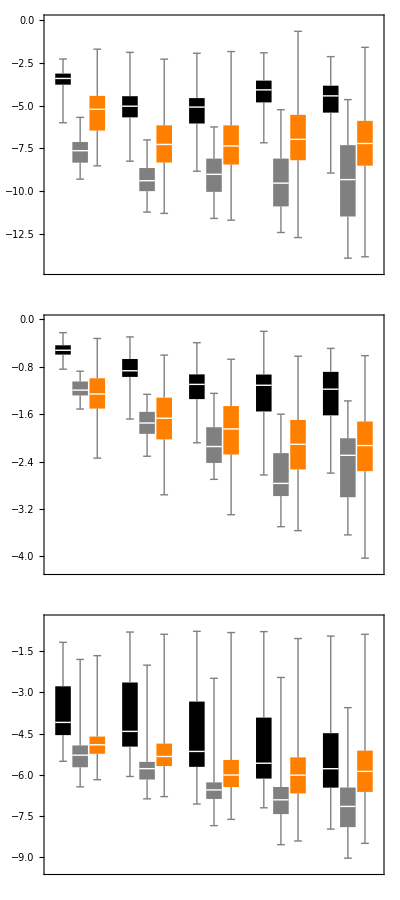

```mathematica
ip = ImagePadding->{{20,5},{5,0}};
F1C3 =Grid[{{BoxWhiskerChart[HH[[{1,2,3}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[1]],ip],BoxWhiskerChart[HH[[{4,5,6}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[2]],ip],BoxWhiskerChart[HH[[{7,8,9}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[3]],ip]}}//Transpose,Spacings->{0,1}]
```

## Figure 1 merge all panels

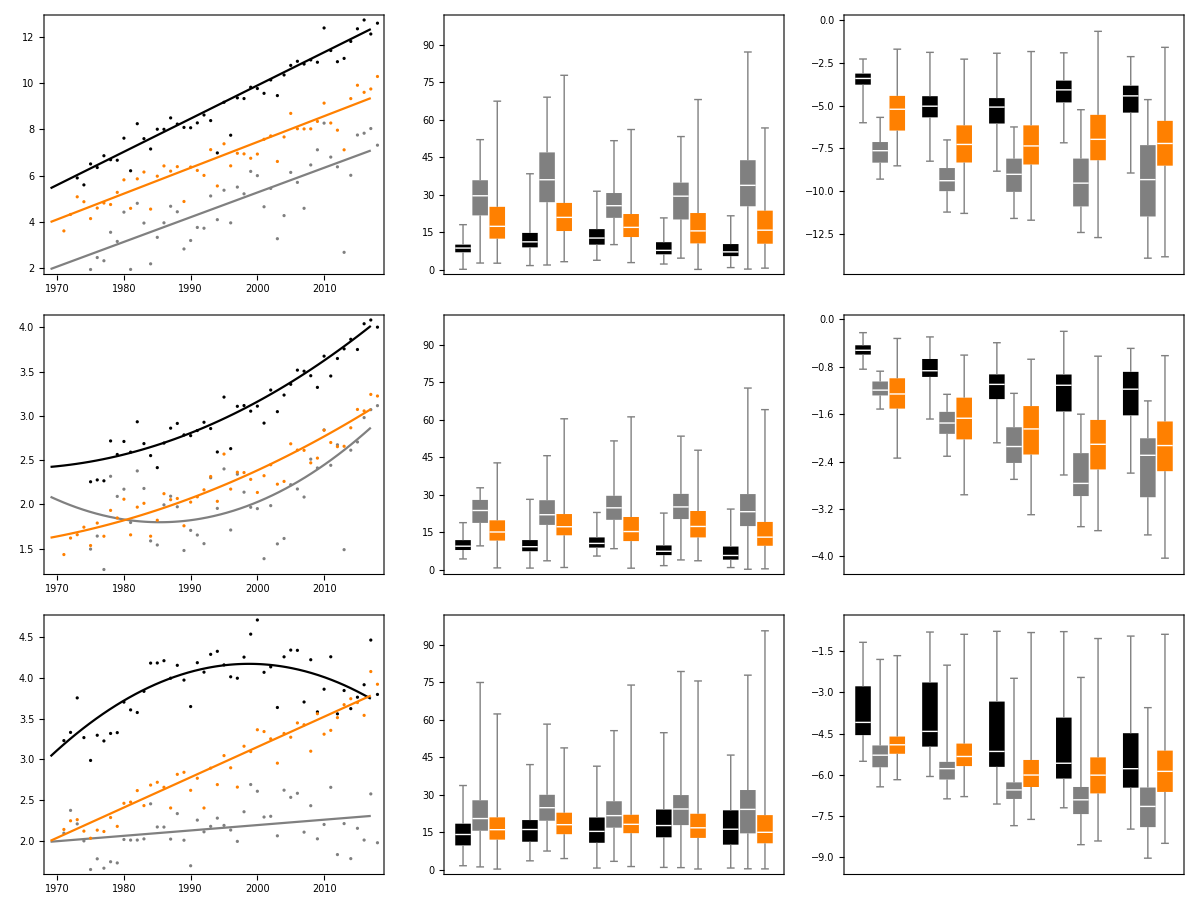

```mathematica
FF1 = Grid[Transpose@{{Show[F1[[1;;3]],PlotRange->All],Show[F1[[4;;6]],PlotRange->All],Show[F1[[7;;9]],PlotRange->All]},
{BoxWhiskerChart[VV[[{1,2,3}]]//Transpose,BarSpacing->{0.1,1},cs,pr2,ip,ImageSize->2.5 72],BoxWhiskerChart[VV[[{4,5,6}]]//Transpose,BarSpacing->{0.1,1},cs,pr2,ip,ImageSize->2.5 72],BoxWhiskerChart[VV[[{7,8,9}]]//Transpose,BarSpacing->{0.1,1},cs,pr2,ip,ImageSize->2.5 72]},{BoxWhiskerChart[HH[[{1,2,3}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[1]],ip,ImageSize->2.5 72],BoxWhiskerChart[HH[[{4,5,6}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[2]],ip,ImageSize->2.5 72],BoxWhiskerChart[HH[[{7,8,9}]]//Transpose,BarSpacing->{0.1,1},cs,pr3[[3]],ip,ImageSize->2.5 72]}},Spacings->{2,1.25}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1.jpg",FF1,ImageResolution->600]
```

/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig1.jpg

## Figure 4

```mathematica
ip = {{25,5},{20,2}};

(* for the actual scatter plot *)
fr = Frame->{{True,False},{True,False}};
prp = PlotRangePadding->Scaled[.075];
imp = ImagePadding->ip;
ims = ImageSize-> 72 3.5;
pm = PlotMarkers-> {"◦",6};
ls = LabelStyle->Directive[FontFamily->"Arial",12];
ls2 = LabelStyle->Directive[FontFamily->"Arial",16];
ps = PlotStyle->Gray;
at = AbsoluteThickness[1.5];
```

```mathematica
FIG= {};
Do[

x1= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_pred_lin.csv"][[All,(1+24)]]/1000.;
x23= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{3,9}]];
x2 = x23[[All,1]];
x3 = x23[[All,2]];

s12 = SpearmanRankTest[x1,x2,"TestDataTable"];
rho12 =Round[s12[[1,1,2,2]],0.001];

s13 = SpearmanRankTest[x1,x3,"TestDataTable"];
rho13 = Round[s13[[1,1,2,2]],0.001];

s23 = SpearmanRankTest[x2,x3,"TestDataTable"];
rho23 = Round[s23[[1,1,2,2]],0.001];

f1 = Labeled[ListPlot[{x1,x2}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho12,ims,ls],{"Mean yield", "Slope"},{ Bottom,Left},RotateLabel->True,ls2];
f2 =Labeled[ ListPlot[{x1,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho13,ims,ls],{"Mean yield", "Variability"},{ Bottom,Left},RotateLabel->True,ls2];
f3 =Labeled[ListPlot[{x2,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho23,ims,ls],{"Slope", "Variability"},{Bottom,Left},RotateLabel->True,ls2];

fig = {f1,f2,f3};

AppendTo[FIG,fig];

,{i,{3,6,9}}](*this is for the all practices indexing*)
```

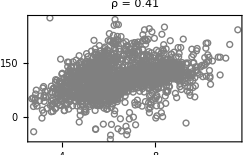
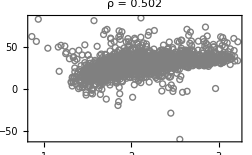
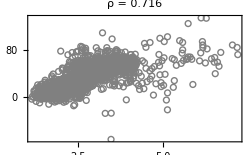
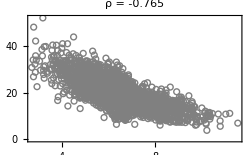
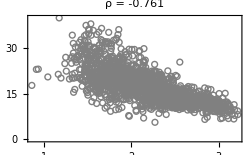
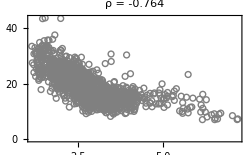
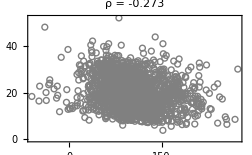
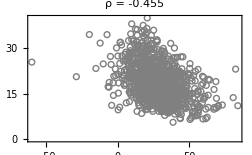
-Graphics-Mean yieldSlope | -Graphics-Mean yieldSlope | -Graphics-Mean yieldSlope
-Graphics-Mean yieldVariability | -Graphics-Mean yieldVariability | -Graphics-Mean yieldVariability
-Graphics-SlopeVariability | -Graphics-SlopeVariability | -Graphics-SlopeVariability

```mathematica
fig4 = Grid[FIG//Transpose,Spacings->{1,1}]
```

```mathematica
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig4.jpg",fig4,ImageResolution->300]
```

/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig4.jpg

```mathematica
FIG= {};
Do[

x1= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_pred_lin.csv"][[All,(1+24)]]/1000.;
x23= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{3,9}]];
x2 = x23[[All,1]];
x3 = x23[[All,2]];

s12 = SpearmanRankTest[x1,x2,"TestDataTable"];
rho12 ={Round[s12[[1,1,2,2]],0.001],s12[[1,1,2,3]]};

s13 = SpearmanRankTest[x1,x3,"TestDataTable"];
rho13 = {Round[s13[[1,1,2,2]],0.001],s13[[1,1,2,3]]};

s23 = SpearmanRankTest[x2,x3,"TestDataTable"];
rho23 = {Round[s23[[1,1,2,2]],0.001],s23[[1,1,2,3]]};

f1 = Labeled[ListPlot[{x1,x2}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho12,ims,ls],{"Mean yield", "Slope"},{ Bottom,Left},RotateLabel->True,ls2];
f2 =Labeled[ ListPlot[{x1,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho13,ims,ls],{"Mean yield", "Variability"},{ Bottom,Left},RotateLabel->True,ls2];
f3 =Labeled[ListPlot[{x2,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho23,ims,ls],{"Slope", "Variability"},{Bottom,Left},RotateLabel->True,ls2];

fig = {f1,f2,f3};

AppendTo[FIG,fig];

,{i,{3,6,9}}](*this is for the all practices indexing*)
```

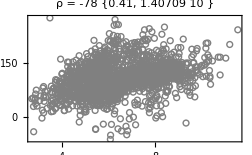
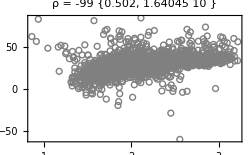
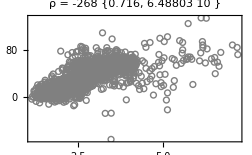
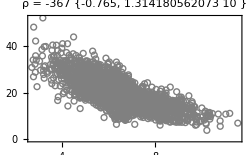
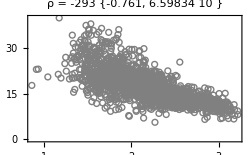
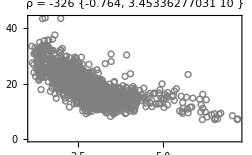
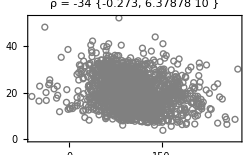
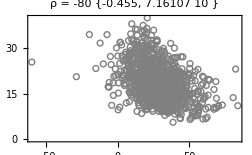
-Graphics-Mean yieldSlope | -Graphics-Mean yieldSlope | -Graphics-Mean yieldSlope
-Graphics-Mean yieldVariability | -Graphics-Mean yieldVariability | -Graphics-Mean yieldVariability
-Graphics-SlopeVariability | -Graphics-SlopeVariability | -Graphics-SlopeVariability

```mathematica
fig4 = Grid[FIG//Transpose,Spacings->{1,1}]
```

### Figures 5 and 6 for Irrigated and non-irrigated

```mathematica
FIG= {};STAT = {};
Do[

x1= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_pred_lin.csv"][[All,(1+24)]]/1000.;
x23= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{3,9}]];
x2 = x23[[All,1]];
x3 = x23[[All,2]];

s12 = SpearmanRankTest[x1,x2,"TestDataTable"];
rho12 =Round[s12[[1,1,2,2]],0.001];
pval12 = NumberForm[s12[[1,1,2,3]],2];
pl12 = {rho12,pval12};

s13 = SpearmanRankTest[x1,x3,"TestDataTable"];
rho13 = Round[s13[[1,1,2,2]],0.001];
pval13 = NumberForm[s13[[1,1,2,3]],2];
pl13 = {rho13,pval13};

s23 = SpearmanRankTest[x2,x3,"TestDataTable"];
rho23 = Round[s23[[1,1,2,2]],0.001];
pval23 = NumberForm[s23[[1,1,2,3]],2];
pl23 = {rho23,pval23};

stat = {pl12,pl13,pl23};AppendTo[STAT,stat];

NS12 = If[i==1, ", NS",""];
NS13 = If[i==4, ", NS",""];

f1 = Labeled[ListPlot[{x1,x2}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho12<>NS12,ims,ls],{"Mean yield", "Slope"},{ Bottom,Left},RotateLabel->True,ls2];
f2 =Labeled[ ListPlot[{x1,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho13<>NS13,ims,ls],{"Mean yield", "Variability"},{ Bottom,Left},RotateLabel->True,ls2];
f3 =Labeled[ListPlot[{x2,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho23,ims,ls],{"Slope", "Variability"},{Bottom,Left},RotateLabel->True,ls2];

fig = {f1,f2,f3};

AppendTo[FIG,fig];

,{i,{1,4,7}}];
fig5 = Grid[FIG//Transpose,Spacings->{1,1}];
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig5.jpg",fig5,ImageResolution->300];
Grid[STAT//Transpose,Frame->All,Spacings->{2,2}]
```

{-0.119,0.067} | {0.261,0.002} | {0.658,1.7×10^-30}
{-0.524,3.4×10^-18} | {-0.148,0.082} | {-0.788,5.6×10^-51}
{-0.249,0.00011} | {-0.334,0.000062} | {-0.584,6.6×10^-23}

```mathematica
FIG= {};STAT = {};
Do[

x1= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_pred_lin.csv"][[All,(1+24)]]/1000.;
x23= Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{3,9}]];
x2 = x23[[All,1]];
x3 = x23[[All,2]];

s12 = SpearmanRankTest[x1,x2,"TestDataTable"];
rho12 =Round[s12[[1,1,2,2]],0.001];
pval12 = NumberForm[s12[[1,1,2,3]],2];
pl12 = {rho12,pval12};

s13 = SpearmanRankTest[x1,x3,"TestDataTable"];
rho13 = Round[s13[[1,1,2,2]],0.001];
pval13 = NumberForm[s13[[1,1,2,3]],2];
pl13 = {rho13,pval13};

s23 = SpearmanRankTest[x2,x3,"TestDataTable"];
rho23 = Round[s23[[1,1,2,2]],0.001];
pval23 = NumberForm[s23[[1,1,2,3]],2];
pl23 = {rho23,pval23};

stat = {pl12,pl13,pl23};AppendTo[STAT,stat];

f1 = Labeled[ListPlot[{x1,x2}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho12,ims,ls],{"Mean yield", "Slope"},{ Bottom,Left},RotateLabel->True,ls2];
f2 =Labeled[ ListPlot[{x1,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho13,ims,ls],{"Mean yield", "Variability"},{ Bottom,Left},RotateLabel->True,ls2];
f3 =Labeled[ListPlot[{x2,x3}//Transpose,Frame->True,PlotRange->All,pm,imp,ps,prp,PlotLabel->"ρ = "<> ToString@rho23,ims,ls],{"Slope", "Variability"},{Bottom,Left},RotateLabel->True,ls2];

fig = {f1,f2,f3};

AppendTo[FIG,fig];

,{i,{2,5,8}}];
fig6 = Grid[FIG//Transpose,Spacings->{1,1}];
Export["/Users/gola/Box Sync/projects/ACES_ag_trends/figs/fig6.jpg",fig6,ImageResolution->200];
Grid[STAT//Transpose,Frame->All,Spacings->{2,2}]
```

{0.693,8.8×10^-30} | {0.557,1.9×10^-13} | {0.432,8.×10^-29}
{-0.719,6.5×10^-33} | {-0.461,3.8×10^-9} | {-0.525,6.1×10^-44}
{-0.691,1.5×10^-29} | {-0.437,2.8×10^-8} | {-0.155,0.00013}

## Figure 5: data compilation

### Sum of high and low scores

```mathematica
(* score each variable with 1 if it is below th 10% quantile and or above the 90% quantile,  the sum of the scores is calculated to see with counties are the worst and the best *)
On[Assert];
allFIPS = {};
Do[
(* combine all variables: slope, acceleration/deceleration, scaled residuals, yield gap for 2008-2017 *)
 dat1 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{1,3,5,9}]]; 
dat2 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap.csv"][[2;;-2,{1,6}]];
temp = Import["/your_directory/clean/clean_"<>NAME[[i]]<>".csv"][[2;;,-10;;]];
temp2=Cases[#,_Real]&/@temp;
dat3 =Partition[ Mean /@ temp2,1];

Assert[Length@dat3 == Length@dat1];

dat4 = Join[dat1,dat2[[All,{-1}]],2];
dat4 = Join[dat4,dat3,2];

(* calculating the 0.1 and 0.9 quantile for each variable *)
minq = maxq = {};
Do[
dd =Cases[dat4[[All,i]],_Real];
AppendTo[minq, Quantile[dd,0.1]];
AppendTo[maxq , Quantile[dd,0.9]];
,{i,2,6}];

newd = dat4[[All,{1}]];
AppendTo[allFIPS, newd];
Do[
vect = dat4[[i,2;;]];
(*calculate the score for counties that are less than the 0.05 quantile *)
resl =ConstantArray[0,5];
resl[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≤  minq[[1]],-1];(* rate of increase *)
resl[[2]] =  If[NumericQ[vect[[2]]]==True &&vect[[2]] ≤  minq[[2]],-1]; (* acceleration or deceleration *)
resl[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]]≥   maxq[[3]],-1]; (* variability, ≥  max used since high is bad *)
resl[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≤  minq[[4]],-1];(* yield gap *)
resl[[5]] =  If[NumericQ[vect[[5]]]==True && vect[[5]]≤  minq[[5]],-1]; (* mean yield during 2008-2017 *)


(*calculate the score for counties that are more than the 0.95 quantile *)
resm =ConstantArray[0,5];
resm[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≥   maxq[[1]],1];
resm[[2]] =  If[NumericQ[vect[[2]]]==True && vect[[2]] ≥  maxq[[2]],1];
resm[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]] ≤  minq[[3]],1];
resm[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≥  maxq[[4]],1];
resm[[5]] =  If[NumericQ[vect[[5]]]==True && vect[[5]]≥  maxq[[5]],1];

score1= Total[Cases[Flatten[{resl[[{1,2,4}]],resm[[{1,2,4}]]}],_Integer]]; (*no acc and dec, no mean yield*)
score2= Total[Cases[Flatten[{resl[[{1,2,4,5}]],resm[[{1,2,4,5}]]}],_Integer]]; (* no mean yield *)
score3= Total[Cases[Flatten[{resl,resm}],_Integer]]; (* all five variables included *)

AppendTo[newd[[i]],score1];
AppendTo[newd[[i]],score2];
AppendTo[newd[[i]],score3];

,{i, Length@dat4}];

PrependTo[newd,{"FIPS","3vars","4vars","5vars"}];
Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_sumscore.csv",newd]; 
,{i,Length@NAME}];
```

```mathematica
(* compile the score data *)
allFIPS = Union[Flatten@allFIPS];
scoresum1 = scoresum2 = scoresum3 = ConstantArray["NA",{Length@allFIPS,10}]; (*scoresumMY, MY is for mean yield *)
scoresum1[[All,1]] = scoresum2[[All,1]] = scoresum3[[All,1]]= allFIPS; 
Do[
dat = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_sumscore.csv"][[2;;]];
Do[
fips = dat[[j,1]];
pos = Position[allFIPS,fips][[1,1]];
scoresum1[[pos,i+1]]= dat[[j,2]];
scoresum2[[pos,i+1]]= dat[[j,3]];
scoresum3[[pos,i+1]]= dat[[j,4]];
,{j,Length@dat}];
,{i,Length@NAME}];
PrependTo[scoresum1,Flatten[{"FIPS",NAME}]];
PrependTo[scoresum2,Flatten[{"FIPS",NAME}]];
PrependTo[scoresum3,Flatten[{"FIPS",NAME}]];
```

```mathematica
Export["/your_directory/clean/clean_sumscore1.csv",scoresum1];
Export["/your_directory/clean/clean_sumscore2.csv",scoresum2];
Export["/your_directory/clean/clean_sumscore3.csv",scoresum3];
```

### Recycle: Rank

```mathematica
(* combine all variables: slope,  scaled residuals, yield gap for 2008-2017 *)
Do[

dat1 = Import["/your_directory/clean/clean_"<>NAME[[ii]]<>"_fit_coeff.csv"][[2;;-2,{1,5,9}]]; 
dat2 = Import["/your_directory/clean/clean_"<>NAME[[ii]]<>"_ygap.csv"][[2;;-2,{1,6}]]; 
dat3 = Join[dat1,dat2[[All,{-1}]],2];

newd = dat3;
newd = Select[newd, NumericQ[Total[#]]==True& ];

Do[
temp = SortBy[newd[[All,{1,j}]],Last];
temp[[All,2]]= Round[temp[[All,2]],0.00001];(* for wheat_unc and yield gap, there is a problem of numerical precision, some val are similar at 10^-16, the union do not find them but the position is less precise resulting in multilple finds, the use of Round chop these numerical errors *)
val = Union@temp[[All,2]];
rank = {};
Do[
vv = val[[i]];
(* the next two lines is aimed at giving the same rank to same values *)
pos = Flatten[Position[temp[[All,2]],vv]];
rr = ConstantArray[pos[[1]],Length@pos];
AppendTo[rank,rr];
,{i,Length@val}];
rank = Flatten@rank;
temp[[All,2]]=If[j==3,Length@temp- rank,rank];(* replace the ordered actual values with the updated ranks, the scaled standard deviation is inversed as high value means low rank *)

Do[
fips = temp[[i,1]];
pos = Position[newd[[All,1]],fips][[1,1]];
newd[[pos,j]]= temp[[i,2]]; (* replace the values from the original data with the rank *)
,{i,Length@temp}];

,{j,{2,3,4}}];

(* calculating the mean rank and ranking with respect to mean rank *)
meanrank = Map[Mean,newd[[All,2;;]]] //N;
nd = Transpose[{newd[[All,1]],meanrank}];

(* the same algorithm as above to rank with potential same rank *)
temp = SortBy[nd,Last];
val = Union[temp[[All,2]]];
rank = {};
Do[
vv = val[[i]];
(* the next two lines is aimed at giving the same rank to same values *)
pos = Flatten[Position[temp[[All,2]],vv]];
rr = ConstantArray[pos[[1]],Length@pos];
AppendTo[rank,rr];
,{i,Length@val}];

rank = Flatten@rank;
temp[[All,2]]=rank;

Do[
fips = temp[[i,1]];
pos = Position[nd[[All,1]],fips][[1,1]];
nd[[pos,2]]= temp[[i,2]]; (* replace the values from the original data with the rank *)
,{i,Length@temp}];

PrependTo[nd,{"FIPS","meanrank"}];
Export["/your_directory/clean/clean_"<>NAME[[ii]]<>"_rank.csv",nd]; 

,{ii, 9}]
```

```mathematica
(* compile the rank data *)
allFIPS = Union[Flatten@allFIPS];
allrank = ConstantArray["NA",{Length@allFIPS,10}];
allrank[[All,1]] = allFIPS; 
Do[
dat = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_rank.csv"][[2;;]];
Do[
fips = dat[[j,1]];
pos = Position[allFIPS,fips][[1,1]];
allrank[[pos,i+1]]= dat[[j,2]];
,{j,Length@dat}];
,{i,Length@NAME}];
PrependTo[allrank,Flatten[{"FIPS",NAME}]];
```

```mathematica
Export["/your_directory/clean/clean_allrank.csv",allrank];
```

### Recycle: Individual high and low scores

#### Without mean yield at year 1994

```mathematica
(* score each variable with 1 if it is below th 10% quantile and or above the 90% quantile,  the sum of the scores is calculated to see with counties are the worst and the best *)

allFIPS = {};
Do[
(* combine all variables: slope, acceleration/deceleration, scaled residuals, yield gap for 2008-2017 *)
dat1 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{1,3,5,9}]]; 
dat2 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap.csv"][[2;;-2,{1,6}]]; 
dat3 = Join[dat1,dat2[[All,{-1}]],2];

(* calculating the 0.1 and 0.9 quantile for each variable *)
minq = maxq = {};
Do[
dd =Cases[dat3[[All,i]],_Real];
AppendTo[ minq, Quantile[dd,0.1]];
AppendTo[maxq , Quantile[dd,0.9]];
,{i,2,5}];

newd = dat3[[All,1]];
AppendTo[allFIPS, newd];
Do[
vect = dat3[[i,2;;]];
(*calculate the score for counties that are less than the 0.05 quantile *)
resl =ConstantArray[0,4];
resl[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≤  minq[[1]],1];
resl[[2]] =  If[NumericQ[vect[[2]]]==True &&vect[[2]] ≤  minq[[2]],1];
resl[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]]≥   maxq[[3]],1];
resl[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≤  minq[[4]],1];

scorel= Total[Cases[resl,_Integer]];
AppendTo[newd[[{i}]],scorel];

(*calculate the score for counties that are more than the 0.95 quantile *)
resm =ConstantArray[0,4];
resm[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≥   maxq[[1]],1];
resm[[2]] =  If[NumericQ[vect[[2]]]==True && vect[[2]] ≥  maxq[[2]],1];
resm[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]] ≤  minq[[3]],1];
resm[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≥  maxq[[4]],1];

scorem= Total[Cases[resm,_Integer]];
AppendTo[newd[[i]],scorem];
,{i, Length@dat3}];

PrependTo[newd,{"FIPS","worstC","bestC"}];
Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_score.csv",newd]; 
,{i,Length@NAME}];
```

```mathematica
(* compile the score data *)
allFIPS = Union[Flatten@allFIPS];
scorelow = scorehigh = ConstantArray["NA",{Length@allFIPS,10}];
scorelow[[All,1]] = scorehigh[[All,1]]= allFIPS; 
Do[
dat = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_score.csv"][[2;;]];
Do[
fips = dat[[j,1]];
pos = Position[allFIPS,fips][[1,1]];
scorelow[[pos,i+1]]= dat[[j,2]];
scorehigh[[pos,i+1]]=dat[[j,3]];
,{j,Length@dat}];
,{i,Length@NAME}];
PrependTo[scorelow,Flatten[{"FIPS",NAME}]];
PrependTo[scorehigh,Flatten[{"FIPS",NAME}]];
```

```mathematica
Export["/your_directory/clean/clean_lowscore.csv",scorelow];
Export["/your_directory/clean/clean_highscore.csv",scorehigh];
```

#### With mean yield at year 1994

```mathematica
(* score each variable with 1 if it is below th 10% quantile and or above the 90% quantile,  the sum of the scores is calculated to see with counties are the worst and the best *)

allFIPS = {};
Do[
(* combine all variables: slope, acceleration/deceleration, scaled residuals, yield gap for 2008-2017 *)
dat0 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_pred_lin.csv"][[2;;-2,{1,3,5,9}]]; ;
dat1 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2,{1,3,5,9}]]; 
dat2 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap.csv"][[2;;-2,{1,6}]]; 
dat3 = Join[dat1,dat2[[All,{-1}]],2];

(* calculating the 0.1 and 0.9 quantile for each variable *)
minq = maxq = {};
Do[
dd =Cases[dat3[[All,i]],_Real];
AppendTo[ minq, Quantile[dd,0.1]];
AppendTo[maxq , Quantile[dd,0.9]];
,{i,2,5}];

newd = dat3[[All,1]];
AppendTo[allFIPS, newd];
Do[
vect = dat3[[i,2;;]];
(*calculate the score for counties that are less than the 0.05 quantile *)
resl =ConstantArray[0,4];
resl[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≤  minq[[1]],1];
resl[[2]] =  If[NumericQ[vect[[2]]]==True &&vect[[2]] ≤  minq[[2]],1];
resl[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]]≥   maxq[[3]],1];
resl[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≤  minq[[4]],1];

scorel= Total[Cases[resl,_Integer]];
AppendTo[newd[[{i}]],scorel];

(*calculate the score for counties that are more than the 0.95 quantile *)
resm =ConstantArray[0,4];
resm[[1]] =  If[NumericQ[vect[[1]]]==True && vect[[1]] ≥   maxq[[1]],1];
resm[[2]] =  If[NumericQ[vect[[2]]]==True && vect[[2]] ≥  maxq[[2]],1];
resm[[3]] =  If[NumericQ[vect[[3]]]==True && vect[[3]] ≤  minq[[3]],1];
resm[[4]] =  If[NumericQ[vect[[4]]]==True && vect[[4]]≥  maxq[[4]],1];

scorem= Total[Cases[resm,_Integer]];
AppendTo[newd[[i]],scorem];
,{i, Length@dat3}];

PrependTo[newd,{"FIPS","worstC","bestC"}];
Export["/your_directory/clean/clean_"<>NAME[[i]]<>"_score.csv",newd]; 
,{i,Length@NAME}];
```

```mathematica
(* compile the score data *)
allFIPS = Union[Flatten@allFIPS];
scorelow = scorehigh = ConstantArray["NA",{Length@allFIPS,10}];
scorelow[[All,1]] = scorehigh[[All,1]]= allFIPS; 
Do[
dat = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_score.csv"][[2;;]];
Do[
fips = dat[[j,1]];
pos = Position[allFIPS,fips][[1,1]];
scorelow[[pos,i+1]]= dat[[j,2]];
scorehigh[[pos,i+1]]=dat[[j,3]];
,{j,Length@dat}];
,{i,Length@NAME}];
PrependTo[scorelow,Flatten[{"FIPS",NAME}]];
PrependTo[scorehigh,Flatten[{"FIPS",NAME}]];
```

```mathematica
Export["/your_directory/clean/clean_lowscore.csv",scorelow];
Export["/your_directory/clean/clean_highscore.csv",scorehigh];
```

## Metadata

```mathematica
(* Find the position of a certain value according to a function Fun_ in the vector dat_ *)
FindPosition[Fun_,dat_]:= Module[{result,poi,pos},
If[MemberQ[dat,"NA"] == True,
poi =   Cases[Fun[dat],_?NumericQ][[1]],
poi =  Fun[dat];
];
pos = Position[dat,poi][[1,1]];
result = pos;
result];

(* Find the position of a certain value according to a function Fun_ in the matrix dat_ *)
FindPositionMat[Fun_,dat_]:= Module[{result,poi,pos},
If[MemberQ[dat,"NA",2] == True,
poi =   Cases[Fun[dat],_?NumericQ][[1]],
poi =  Fun[dat];
];
pos = Position[dat,poi][[1]];
result = pos;
result];
```

```mathematica
METADATA={};
Do[
(* imports raw yield data *)
dat1 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>".m"];len = Length@dat1;
(* maximum yield *)
max = Cases[Max[dat1],_?NumericQ][[1]]; 
posmax = Position[dat1,max][[All,All,1]][[1]];
max = {max/1000,posmax}//Flatten;(* the division converts kg to ton*)
(* minimum yield *)
min = Cases[Min[dat1],_?NumericQ][[1]];
posmin = Position[dat1,min][[All,All,1]][[1]];
min= {min/1000,posmin}//Flatten; (* the division converts kg to ton*)

(* imports inferred parameters and fitted value data *)
dat2 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_fit_coeff.csv"][[2;;-2]]; (*because the last one is in Alaska *) 

(* for the linear model *)
pos1 = FindPosition[Max, dat2[[All,3]]];
maxlin = dat2[[pos1,{3,1}]]/{1000,1};
pos2 = FindPosition[Min, dat2[[All,3]]];
minlin = dat2[[pos2,{3,1}]]/{1000,1};

(* for the quadratic model *)
pos3 = FindPosition[Max, dat2[[All,5]]];
maxqua = dat2[[pos3,{5,1}]]/{1000,1};
pos4 = FindPosition[Min, dat2[[All,5]]];
minqua = dat2[[pos4,{5,1}]]/{1000,1};

(* for relative instability *)
pos5 = FindPosition[Max, dat2[[All,9]]];
maxssd = dat2[[pos5,{9,1}]]/{1000,1};
pos6 = FindPosition[Min, dat2[[All,9]]];
minssd = dat2[[pos6,{9,1}]]/{1000,1};

(* for instability *)
pos7 = FindPosition[Max, dat2[[All,6]]];
maxsd = dat2[[pos7,{6,1}]]/{1000,1};
pos8 = FindPosition[Min, dat2[[All,6]]];
minsd = dat2[[pos8,{6,1}]]/{1000,1};

(* for positive instability *)
pos9 = FindPosition[Max, dat2[[All,7]]];
maxresp = dat2[[pos9,{7,1}]]/{1000,1};
pos10 = FindPosition[Min, dat2[[All,7]]];
minresp = dat2[[pos10,{7,1}]]/{1000,1};

(* for negative instability *)
pos11 = FindPosition[Max, dat2[[All,8]]];
maxresn = dat2[[pos11,{8,1}]]/{1000,1};
pos12 = FindPosition[Min, dat2[[All,7]]];
minresn = dat2[[pos12,{8,1}]]/{1000,1};

(* import data from calculated yield gap *)
dat3 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_ygap.csv"];
subdat3 = dat3[[2;;,2;;]];

(* for maximum yield gap *)
pos13= FindPositionMat[Min,subdat3]+1; (* +1 one because we go back to coordinate in dat3 *)
maxyg = {dat3[[pos13[[1]],{pos13[[2]],1}]]/{1000,1},dat3[[1,pos13[[2]]]]}//Flatten;

dat4 = Import["/your_directory/clean/clean_"<>NAME[[i]]<>"_15_sum.csv"][[2;;]];

(* for average yield *)
pos14 = FindPosition[Max, dat4[[All,2]]];
maxay= dat4[[pos14,{2,1}]]/{1000,1};
pos15 = FindPosition[Min, dat4[[All,2]]];
minay= dat4[[pos15,{2,1}]]/{1000,1};

vect = <|"length"-> len, "max"-> max, "min" -> min, "maxlin"->maxlin, "minlin" -> minlin,  "maxqua"->maxqua, "minqua" -> minqua,"maxssd"-> maxssd,"minssd"-> minssd,"maxsd"-> maxsd,"minsd"-> minsd,"maxresp"-> maxresp,"minresp"-> minresp, "maxresn"-> maxresn,"minresn"-> minresn,"maxyg"-> maxyg,"maxay"-> maxay, "minay"-> minay |>;
AppendTo[METADATA,NAME[[i]]-> vect ];
,{i,9}]
```

```mathematica
FMETA = Dataset@Transpose@Association@METADATA
```

Dataset[<>]

```mathematica
Export["/your_directory/clean/metadata.m",FMETA]
```